```mathematica
domSize=50;
cells = 500;
delx=domSize/cells;

pGrid=Table[delx/2+ii delx,{ii,0,cells-1}];

pCharge=Table[0,{ii,0,cells-1}];
```

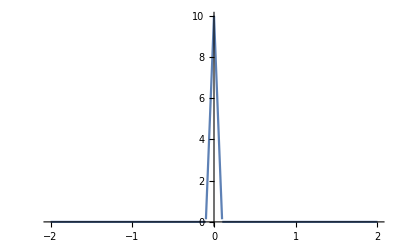

```mathematica
S[r_,rc_]=If[r^2<rc^2,(-Abs[r]+rc)rc^-2,0];
Plot[S[r,0.1],{r,-2,2}]
```

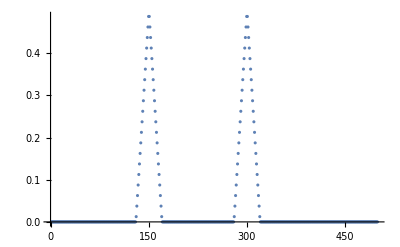

```mathematica
k1=15;
k2=30;
cut=2;
For[i=1,i<cells,i++,
pCharge[[i]]=S[pGrid[[i]]-k1,cut];
pCharge[[i]]=pCharge[[i]]+S[pGrid[[i]]-k2,cut]
];
ListPlot[pCharge,PlotRange->All]
```

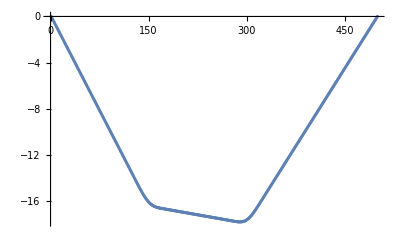

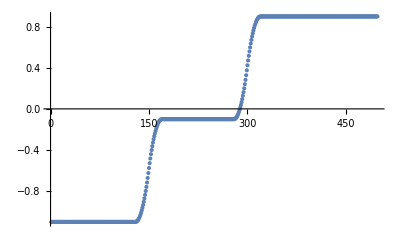

```mathematica
system=Flatten[{Subscript[ϕ, 1]==0,Table[(Subscript[ϕ, ii-1]-2 Subscript[ϕ, ii]+Subscript[ϕ, ii+1])/delx^2==pCharge[[ii]],{ii,2,cells-1}],Subscript[ϕ, cells]==0}];
phi=Solve[system][[1,All,2]];
ef=Table[(phi[[ii+1]]-phi[[ii-1]])/(2 delx),{ii,2,cells-1}];
ListPlot[phi,PlotRange->All]
ListPlot[ef,PlotRange->All]
```